```mathematica
Solve[-1/12==1/2 n(n+1.)]
```

{{n→-0.788675},{n→-0.211325}}

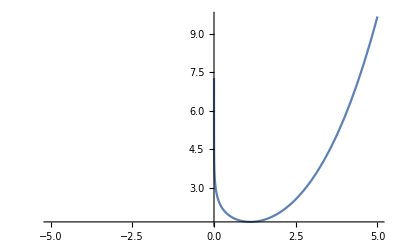

```mathematica
F[x_]:=Log[x]
Plot[(X^2+9 y0^2-6 y0 F[X]+F[X]^2)/(6 y0-2 F[X])/.y0->1,{X,-5,5}]
```

```mathematica
Clear["Global`*"]
θ=ArcTan[(X)/(F[X]-y0)]
Y0P==X/Tan[θ]
h0p==√(y1^2-X^2)
h0pp==h0-h0p
y0pp==y0-y0p


y1==y0pp+h0pp
y1==(y0-X/Tan[θ])+(y0-√(y1^2-X^2))
Solve[y1==(y0-X/Tan[θ])+(y0-√(y1^2-X^2)),y1]
```

ArcTan[X/(-y0+F[X])]

Y0P==-y0+F[X]

h0p==√(-X^2+y1^2)

h0pp==h0-h0p

y0pp==y0-y0p

y1==h0pp+y0pp

y1==3 y0-√(-X^2+y1^2)-F[X]

{{y1→(X^2+9 y0^2-6 y0 F[X]+F[X]^2)/(6 y0-2 F[X])}}